```mathematica
Integrate[(c*x+Q*L-(e*A*Q*(A+Q)/(c^2*b+e*A*(A+Q)))*L)*P*Exp[-x^2/(b/A)],{x,-∞,ω}]
```

```mathematica
1/2 c P (-b/A+(b-b ⅇ^(-(A ω^2)/b))/A+(b c L √π Q (1/(√(A/b))+(ω Erf[√((A ω^2)/b)])/(√((A ω^2)/b))))/(b c^2+A e (A+Q)))/.ω->((e*A*Q(A+Q))/(c^3*b+e*A*c*(A+Q))-Q/c)*L
```

1/2 c P (-b/A+(b-b ⅇ^(-(A L^2 (-Q/c+(A e Q (A+Q))/(b c^3+A c e (A+Q)))^2)/b))/A+(b c L √π Q (1/(√(A/b))+(L (-Q/c+(A e Q (A+Q))/(b c^3+A c e (A+Q))) Erf[√((A L^2 (-Q/c+(A e Q (A+Q))/(b c^3+A c e (A+Q)))^2)/b)])/(√((A L^2 (-Q/c+(A e Q (A+Q))/(b c^3+A c e (A+Q)))^2)/b))))/(b c^2+A e (A+Q)))

```mathematica
Simplify[%2]
```

1/2 c P (-b/A+(b-b ⅇ^(-(A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)))/A+(b c L √π Q (1/(√(A/b))-(b c L Q Erf[√((A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2))])/(√((A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)) (b c^2+A e (A+Q)))))/(b c^2+A e (A+Q)))

```mathematica
Integrate[(c*x-q*l+(e*a*q*(a+q)/(c^2*b+e*a*(a+q)))*l)*p*Exp[-x^2/(b/a)],{x,Ω,∞}]
```

```mathematica
1/2 c p (b/a-(b-b ⅇ^(-(a Ω^2)/b))/a-(b c l √π q (1/(√(a/b))-(Ω Erf[√((a Ω^2)/b)])/(√((a Ω^2)/b))))/(b c^2+a e (a+q)))/.Ω->((e*a*q(a+q))/(c^3*b+e*a*c*(a+q))-q/c)*(-l)
```

1/2 c p (b/a-(b-b ⅇ^(-(a l^2 (-q/c+(a e q (a+q))/(b c^3+a c e (a+q)))^2)/b))/a-(b c l √π q (1/(√(a/b))+(l (-q/c+(a e q (a+q))/(b c^3+a c e (a+q))) Erf[√((a l^2 (-q/c+(a e q (a+q))/(b c^3+a c e (a+q)))^2)/b)])/(√((a l^2 (-q/c+(a e q (a+q))/(b c^3+a c e (a+q)))^2)/b))))/(b c^2+a e (a+q)))

```mathematica
Simplify[%5]
```

1/2 c p (b/a-(b-b ⅇ^(-(a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)))/a-(b c l √π q (1/(√(a/b))-(b c l q Erf[√((a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2))])/(√((a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)) (b c^2+a e (a+q)))))/(b c^2+a e (a+q)))

```mathematica
Simplify[1/2 c p (b/a-(b-b ⅇ^(-(a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)))/a-(b c l √π q (1/(√(a/b))-(b c l q Erf[√((a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2))])/(√((a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)) (b c^2+a e (a+q)))))/(b c^2+a e (a+q)))+1/2 c P (-b/A+(b-b ⅇ^(-(A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)))/A+(b c L √π Q (1/(√(A/b))-(b c L Q Erf[√((A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2))])/(√((A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)) (b c^2+A e (A+Q)))))/(b c^2+A e (A+Q)))]
```

```mathematica
FullSimplify[1/2 c p (b/a-(b-b ⅇ^(-(a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)))/a-(b c l √π q (1/(√(a/b))-(b c l q Erf[√((a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2))])/(√((a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)) (b c^2+a e (a+q)))))/(b c^2+a e (a+q)))+1/2 c P (-b/A+(b-b ⅇ^(-(A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)))/A+(b c L √π Q (1/(√(A/b))-(b c L Q Erf[√((A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2))])/(√((A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)) (b c^2+A e (A+Q)))))/(b c^2+A e (A+Q)))]
```

1/2 b c ((ⅇ^(-(a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)) p)/a-(ⅇ^(-(A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)) P)/A-(c l p √π q)/(√(a/b) (b c^2+a e (a+q)))+(c L P √π Q)/(√(A/b) (b c^2+A e (A+Q)))+√b c √π ((l p q Erf[(√a √b c l q)/(b c^2+a e (a+q))])/(√a (b c^2+a e (a+q)))-(L P Q Erf[(√A √b c L Q)/(b c^2+A e (A+Q))])/(√A (b c^2+A e (A+Q)))))

```mathematica
Subscript[g, l] := π/(2 Subscript[a, l])*Sqrt[(c^2b^2+e*Subscript[a, l]*(Subscript[a, l]+Subscript[d, l]))/(Subscript[d, l]*(Subscript[a, l]+Subscript[d, l]))]*Erf[L*Sqrt[(Subscript[d, l]*Subscript[a, l]*(Subscript[a, l]+Subscript[d, l]))/(c^2*b+e*Subscript[d, l]*(Subscript[a, l]+Subscript[d, l]))]]
```

```mathematica
Subscript[g, r] := π/(2 Subscript[a, r])*Sqrt[(c^2b^2+e*Subscript[a, r]*(Subscript[a, r]+Subscript[d, r]))/(Subscript[d, r]*(Subscript[a, r]+Subscript[d, r]))]*Erf[l*Sqrt[(Subscript[d, r]*Subscript[a, r]*(Subscript[a, r]+Subscript[d, r]))/(c^2*b+e*Subscript[d, r]*(Subscript[a, r]+Subscript[d, r]))]]
```

```mathematica
Solve[{Subscript[A, l]/Subscript[A, r]==Sqrt[Subscript[a, l]/Subscript[a, r]],Subscript[A, l]*Subscript[g, l]+Subscript[A, r]*Subscript[g, r]==1},{Subscript[A, l],Subscript[A, r]}]
```

{{A_l→(2 a_l √(a_l/a_r) a_r)/(π (Erf[L √((a_l d_l (a_l+d_l))/(b c^2+e d_l (a_l+d_l)))] √(a_l/a_r) a_r √((b^2 c^2+e a_l^2+e a_l d_l)/(d_l (a_l+d_l)))+Erf[l √((a_r d_r (a_r+d_r))/(b c^2+e d_r (a_r+d_r)))] a_l √((b^2 c^2+e a_r^2+e a_r d_r)/(d_r (a_r+d_r))))),A_r→(2 a_l a_r)/(π (Erf[L √((a_l d_l (a_l+d_l))/(b c^2+e d_l (a_l+d_l)))] √(a_l/a_r) a_r √((b^2 c^2+e a_l^2+e a_l d_l)/(d_l (a_l+d_l)))+Erf[l √((a_r d_r (a_r+d_r))/(b c^2+e d_r (a_r+d_r)))] a_l √((b^2 c^2+e a_r^2+e a_r d_r)/(d_r (a_r+d_r)))))}}

```mathematica
1/2 b c ((ⅇ^(-(a b c^2 l^2 q^2)/((b c^2+a e (a+q))^2)) p)/a-(ⅇ^(-(A b c^2 L^2 Q^2)/((b c^2+A e (A+Q))^2)) P)/A-(c l p √π q)/(√(a/b) (b c^2+a e (a+q)))+(c L P √π Q)/(√(A/b) (b c^2+A e (A+Q)))+√b c √π ((l p q Erf[(√a √b c l q)/(b c^2+a e (a+q))])/(√a (b c^2+a e (a+q)))-(L P Q Erf[(√A √b c L Q)/(b c^2+A e (A+Q))])/(√A (b c^2+A e (A+Q)))))/.{q->Subscript[d, l],Q->Subscript[d, r],a->Subscript[a, l],A->Subscript[a, r]}
```

1/2 b c ((ⅇ^(-(b c^2 l^2 a_l d_l^2)/((b c^2+e a_l (a_l+d_l))^2)) p)/a_l-(ⅇ^(-(b c^2 L^2 a_r d_r^2)/((b c^2+e a_r (a_r+d_r))^2)) P)/a_r-(c l p √π d_l)/(√(a_l/b) (b c^2+e a_l (a_l+d_l)))+(c L P √π d_r)/(√(a_r/b) (b c^2+e a_r (a_r+d_r)))+√b c √π ((l p Erf[(√b c l √a_l d_l)/(b c^2+e a_l (a_l+d_l))] d_l)/(√a_l (b c^2+e a_l (a_l+d_l)))-(L P Erf[(√b c L √a_r d_r)/(b c^2+e a_r (a_r+d_r))] d_r)/(√a_r (b c^2+e a_r (a_r+d_r)))))

```mathematica
1/2 b c ((ⅇ^(-(b c^2 l^2 Subscript[a, l] Subscript[d, l]^2)/((b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))^2)) p)/Subscript[a, l]-(ⅇ^(-(b c^2 L^2 Subscript[a, r] Subscript[d, r]^2)/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)) P)/Subscript[a, r]-(c l p √π Subscript[d, l])/(√(Subscript[a, l]/b) (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+(c L P √π Subscript[d, r])/(√(Subscript[a, r]/b) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))+√b c √π ((l p Erf[(√b c l √Subscript[a, l] Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))] Subscript[d, l])/(√Subscript[a, l] (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))-(L P Erf[(√b c L √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] Subscript[d, r])/(√Subscript[a, r] (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))))/.{p->Subscript[A, l]*Exp[-L^2*2*Subscript[a, l]*Subscript[d, l]*(Subscript[a, l]+Subscript[d, l])/(e*Subscript[a, l]*(Subscript[a, l]+Subscript[d, l])+c^2*b)],P->Subscript[A, r]*Exp[-l^2*2*Subscript[a, r]*Subscript[d, r]*(Subscript[a, r]+Subscript[d, r])/(e*Subscript[a, r]*(Subscript[a, r]+Subscript[d, r])+c^2*b)]}
```

```mathematica
1/2 b c ((ⅇ^(-(b c^2 l^2 Subscript[a, l] Subscript[d, l]^2)/((b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))^2)-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) Subscript[A, l])/Subscript[a, l]-(ⅇ^(-(b c^2 L^2 Subscript[a, r] Subscript[d, r]^2)/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) Subscript[A, r])/Subscript[a, r]-(c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π Subscript[A, l] Subscript[d, l])/(√(Subscript[a, l]/b) (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+(c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π Subscript[A, r] Subscript[d, r])/(√(Subscript[a, r]/b) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))+√b c √π ((ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l Erf[(√b c l √Subscript[a, l] Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))] Subscript[A, l] Subscript[d, l])/(√Subscript[a, l] (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))-(ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L Erf[(√b c L √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] Subscript[A, r] Subscript[d, r])/(√Subscript[a, r] (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))))/.{{Subscript[A, l]->(2 Subscript[a, l] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r])/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))))),Subscript[A, r]->(2 Subscript[a, l] Subscript[a, r])/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))))}}
```

```mathematica
FullSimplify[1/2 b c (-((2 ⅇ^(-(b c^2 L^2 Subscript[a, r] Subscript[d, r]^2)/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) Subscript[a, l])/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))))))+(2 ⅇ^(-(b c^2 l^2 Subscript[a, l] Subscript[d, l]^2)/((b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))^2)-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r])/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))))-(2 c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l Subscript[a, l] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] Subscript[d, l])/(√π √(Subscript[a, l]/b) (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])) (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))))+(2 c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L Subscript[a, l] Subscript[a, r] Subscript[d, r])/(√π √(Subscript[a, r]/b) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])) (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))))+√b c √π ((2 ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l Erf[(√b c l √Subscript[a, l] Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))] √Subscript[a, l] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] Subscript[d, l])/(π (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])) (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))))-(2 ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L Erf[(√b c L √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] Subscript[a, l] √Subscript[a, r] Subscript[d, r])/(π (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])) (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((b^2 c^2+e Subscript[a, l]^2+e Subscript[a, l] Subscript[d, l])/(Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((b^2 c^2+e Subscript[a, r]^2+e Subscript[a, r] Subscript[d, r])/(Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))))))]
```

```mathematica
Series[(b c ((√b c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π Erf[(√b c l √Subscript[a, l] Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))] Subscript[a, l]^(3/2) Subscript[d, l])/(√(Subscript[a, l]/Subscript[a, r])*(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+√(Subscript[a, l]/Subscript[a, r])* Subscript[a, r] (ⅇ^(-(Subscript[a, l] Subscript[d, l] (b c^2 l^2 Subscript[d, l]+2 L^2 (Subscript[a, l]+Subscript[d, l]) (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))))/((b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))^2))-(b c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π √(Subscript[a, l]/b) Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+1/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))Subscript[a, l] (-√b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π Erf[(√b c L √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] √Subscript[a, r] Subscript[d, r]+b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π √(Subscript[a, r]/b) Subscript[d, r]-ⅇ^(-(Subscript[a, r] Subscript[d, r] (b c^2 L^2 Subscript[d, r]+2 l^2 (Subscript[a, r]+Subscript[d, r]) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))))/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))))/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r])* Subscript[a, r] √((e Subscript[a, l]+(b^2 c^2)/(Subscript[a, l]+Subscript[d, l]))/Subscript[d, l])+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((e Subscript[a, r]+(b^2 c^2)/(Subscript[a, r]+Subscript[d, r]))/Subscript[d, r]))),{c,0,4}]
```

(b (-ⅇ^(-(2 l^2 d_r)/e) a_l+ⅇ^(-(2 L^2 d_l)/e) √(a_l/a_r) a_r) c)/(π (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)))+(b (-(b ⅇ^(-(2 L^2 d_l)/e) l √π √(a_l/b) √(a_l/a_r) a_r d_l)/(e a_l (a_l+d_l))+(b ⅇ^(-(2 l^2 d_r)/e) L √π a_l √(a_r/b) d_r)/(e a_r (a_r+d_r))) c^2)/(π (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)))+1/π b (((-ⅇ^(-(2 l^2 d_r)/e) a_l+ⅇ^(-(2 L^2 d_l)/e) √(a_l/a_r) a_r) (-(b^2 Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l))/(2 e a_l (a_l+d_l) (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)))+(b ⅇ^(-(L^2 a_l)/e) L √(a_l/e) √(a_l/a_r) a_r √((e a_l)/d_l))/(e √π d_l (a_l+d_l) (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)))-(b^2 Erf[l √(a_r/e)] a_l √((e a_r)/d_r))/(2 e a_r (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)) (a_r+d_r))+(b ⅇ^(-(l^2 a_r)/e) l a_l √(a_r/e) √((e a_r)/d_r))/(e √π (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)) d_r (a_r+d_r))))/(Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r))+((2 b ⅇ^(-(2 L^2 d_l)/e) l^2 d_l^2)/(e^2 √(a_l/a_r) (a_l+d_l)^2)+(b ⅇ^(-(2 L^2 d_l)/e) √(a_l/a_r) a_r d_l (2 L^2 a_l-l^2 d_l+2 L^2 d_l))/(e^2 a_l (a_l+d_l)^2)-(b ⅇ^(-(2 l^2 d_r)/e) a_l d_r (2 l^2 a_r+2 l^2 d_r+L^2 d_r))/(e^2 a_r (a_r+d_r)^2))/(Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r))) c^3+1/π b (((-(b^2 Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l))/(2 e a_l (a_l+d_l) (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)))+(b ⅇ^(-(L^2 a_l)/e) L √(a_l/e) √(a_l/a_r) a_r √((e a_l)/d_l))/(e √π d_l (a_l+d_l) (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)))-(b^2 Erf[l √(a_r/e)] a_l √((e a_r)/d_r))/(2 e a_r (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)) (a_r+d_r))+(b ⅇ^(-(l^2 a_r)/e) l a_l √(a_r/e) √((e a_r)/d_r))/(e √π (Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r)) d_r (a_r+d_r))) (-(b ⅇ^(-(2 L^2 d_l)/e) l √π √(a_l/b) √(a_l/a_r) a_r d_l)/(e a_l (a_l+d_l))+(b ⅇ^(-(2 l^2 d_r)/e) L √π a_l √(a_r/b) d_r)/(e a_r (a_r+d_r))))/(Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r))+((b^2 ⅇ^(-(2 L^2 d_l)/e) l √π √(a_l/b) √(a_l/a_r) a_r d_l (e-2 L^2 d_l))/(e^3 a_l^2 (a_l+d_l)^2)-(b^2 ⅇ^(-(2 l^2 d_r)/e) L √π a_l √(a_r/b) d_r (e-2 l^2 d_r))/(e^3 a_r^2 (a_r+d_r)^2))/(Erf[L √(a_l/e)] √(a_l/a_r) a_r √((e a_l)/d_l)+Erf[l √(a_r/e)] a_l √((e a_r)/d_r))) c^4+O[c]^5

```mathematica
(b c ((√b c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π Erf[(√b c l √Subscript[a, l] Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))] Subscript[a, l]^(3/2) Subscript[d, l])/(√(Subscript[a, l]/Subscript[a, r])*(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+√(Subscript[a, l]/Subscript[a, r])* Subscript[a, r] (ⅇ^(-(Subscript[a, l] Subscript[d, l] (b c^2 l^2 Subscript[d, l]+2 L^2 (Subscript[a, l]+Subscript[d, l]) (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))))/((b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))^2))-(b c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π √(Subscript[a, l]/b) Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+1/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))Subscript[a, l] (-√b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π Erf[(√b c L √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] √Subscript[a, r] Subscript[d, r]+b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π √(Subscript[a, r]/b) Subscript[d, r]-ⅇ^(-(Subscript[a, r] Subscript[d, r] (b c^2 L^2 Subscript[d, r]+2 l^2 (Subscript[a, r]+Subscript[d, r]) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))))/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))))/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r])* Subscript[a, r] √((e Subscript[a, l]+(b^2 c^2)/(Subscript[a, l]+Subscript[d, l]))/Subscript[d, l])+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((e Subscript[a, r]+(b^2 c^2)/(Subscript[a, r]+Subscript[d, r]))/Subscript[d, r])))/.{c->0}
```

0

```mathematica
FullSimplify[(b c ((√b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) l √π Erf[(√b c l √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] Subscript[a, r]^(3/2) Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))+Subscript[a, r] (ⅇ^(-(Subscript[a, r] Subscript[d, r] (b c^2 l^2 Subscript[d, r]+2 l^2 (Subscript[a, r]+Subscript[d, r]) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))))/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2))-(b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) l √π √(Subscript[a, r]/b) Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))+1/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))Subscript[a, r] (-√b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) l √π Erf[(√b c l √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] √Subscript[a, r] Subscript[d, r]+b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) l √π √(Subscript[a, r]/b) Subscript[d, r]-ⅇ^(-(Subscript[a, r] Subscript[d, r] (b c^2 l^2 Subscript[d, r]+2 l^2 (Subscript[a, r]+Subscript[d, r]) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))))/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))))/(2 π Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, r] √((e Subscript[a, r]+(b^2 c^2)/(Subscript[a, r]+Subscript[d, r]))/Subscript[d, r]))]
```

0

```mathematica
(b c ((√b c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π Erf[(√b c l √Subscript[a, l] Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))] Subscript[a, l]^(3/2) Subscript[d, l])/(√(Subscript[a, l]/Subscript[a, r])*(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+√(Subscript[a, l]/Subscript[a, r])* Subscript[a, r] (ⅇ^(-(Subscript[a, l] Subscript[d, l] (b c^2 l^2 Subscript[d, l]+2 L^2 (Subscript[a, l]+Subscript[d, l]) (b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))))/((b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))^2))-(b c ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))) l √π √(Subscript[a, l]/b) Subscript[d, l])/(b c^2+e Subscript[a, l] (Subscript[a, l]+Subscript[d, l])))+1/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))Subscript[a, l] (-√b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π Erf[(√b c L √Subscript[a, r] Subscript[d, r])/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))] √Subscript[a, r] Subscript[d, r]+b c ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))) L √π √(Subscript[a, r]/b) Subscript[d, r]-ⅇ^(-(Subscript[a, r] Subscript[d, r] (b c^2 L^2 Subscript[d, r]+2 l^2 (Subscript[a, r]+Subscript[d, r]) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))))/((b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))^2)) (b c^2+e Subscript[a, r] (Subscript[a, r]+Subscript[d, r])))))/(π (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(b c^2+e Subscript[d, l] (Subscript[a, l]+Subscript[d, l])))] √(Subscript[a, l]/Subscript[a, r])* Subscript[a, r] √((e Subscript[a, l]+(b^2 c^2)/(Subscript[a, l]+Subscript[d, l]))/Subscript[d, l])+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(b c^2+e Subscript[d, r] (Subscript[a, r]+Subscript[d, r])))] Subscript[a, l] √((e Subscript[a, r]+(b^2 c^2)/(Subscript[a, r]+Subscript[d, r]))/Subscript[d, r])))/.{c->δT*k/(2*γ*T),b->4*T/γ,e->(T^2-(δT)^2)/(γ*T)}
```

```mathematica
(2 k δT ((ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ))) k l √π √(T/γ) δT Erf[(k l √(T/γ) δT √Subscript[a, l] Subscript[d, l])/(T γ ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ)))] Subscript[a, l]^(3/2) Subscript[d, l])/(T γ √(Subscript[a, l]/Subscript[a, r]) ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ)))+√(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] (ⅇ^(-(Subscript[a, l] Subscript[d, l] ((k^2 l^2 δT^2 Subscript[d, l])/(T γ^3)+2 L^2 (Subscript[a, l]+Subscript[d, l]) ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ))))/(((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ))^2))-(ⅇ^(-(2 L^2 Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ))) k l √π δT √((γ Subscript[a, l])/T) Subscript[d, l])/(γ^2 ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, l] (Subscript[a, l]+Subscript[d, l]))/(T γ))))+(Subscript[a, l] (-(ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ))) k L √π √(T/γ) δT Erf[(k L √(T/γ) δT √Subscript[a, r] Subscript[d, r])/(T γ ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ)))] √Subscript[a, r] Subscript[d, r])/(T γ)+(ⅇ^(-(2 l^2 Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ))) k L √π δT √((γ Subscript[a, r])/T) Subscript[d, r])/γ^2-ⅇ^(-(Subscript[a, r] Subscript[d, r] ((k^2 L^2 δT^2 Subscript[d, r])/(T γ^3)+2 l^2 (Subscript[a, r]+Subscript[d, r]) ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ))))/(((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ))^2)) ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ))))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[a, r] (Subscript[a, r]+Subscript[d, r]))/(T γ))))/(π γ^2 (Erf[L √((Subscript[a, l] Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[d, l] (Subscript[a, l]+Subscript[d, l]))/(T γ)))] √(Subscript[a, l]/Subscript[a, r]) Subscript[a, r] √((((T^2-δT^2) Subscript[a, l])/(T γ)+(4 k^2 δT^2)/(γ^4 (Subscript[a, l]+Subscript[d, l])))/Subscript[d, l])+Erf[l √((Subscript[a, r] Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[d, r] (Subscript[a, r]+Subscript[d, r]))/(T γ)))] Subscript[a, l] √((((T^2-δT^2) Subscript[a, r])/(T γ)+(4 k^2 δT^2)/(γ^4 (Subscript[a, r]+Subscript[d, r])))/Subscript[d, r])))/.{Subscript[a, l]->2*(k+Subscript[k, l])/γ,Subscript[a, r]->2*(k+Subscript[k, r])/γ,Subscript[d, l]->Subscript[k, l]/γ,Subscript[d, r]->Subscript[k, r]/γ}
```

```mathematica
Simplify[(2 k δT ((2 ⅇ^(-(4 L^2 Subscript[k, l] (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2)))) k l √(2 π) √(T/γ) δT Erf[(√2 k l √(T/γ) δT Subscript[k, l] √((k+Subscript[k, l])/γ))/(T γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2)))] Subscript[k, l] ((k+Subscript[k, l])/γ)^(3/2))/(T γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2)) √((k+Subscript[k, l])/(k+Subscript[k, r])))+(2 (ⅇ^(-(2 Subscript[k, l] (k+Subscript[k, l]) ((k^2 l^2 δT^2 Subscript[k, l])/(T γ^4)+2 L^2 (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ) ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2))))/(γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2))^2))-(ⅇ^(-(4 L^2 Subscript[k, l] (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2)))) k l √(2 π) δT Subscript[k, l] √((k+Subscript[k, l])/T))/(γ^3 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2)))) √((k+Subscript[k, l])/(k+Subscript[k, r])) (k+Subscript[k, r]))/γ+1/(γ ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2)))2 (k+Subscript[k, l]) ((ⅇ^(-(4 l^2 Subscript[k, r] (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2)))) k L √(2 π) δT Subscript[k, r] √((k+Subscript[k, r])/T))/γ^3-(ⅇ^(-(4 l^2 Subscript[k, r] (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2)))) k L √(2 π) √(T/γ) δT Erf[(√2 k L √(T/γ) δT Subscript[k, r] √((k+Subscript[k, r])/γ))/(T γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2)))] Subscript[k, r] √((k+Subscript[k, r])/γ))/(T γ^2)-ⅇ^(-(2 Subscript[k, r] (k+Subscript[k, r]) ((k^2 L^2 δT^2 Subscript[k, r])/(T γ^4)+2 l^2 (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ) ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2))))/(γ^2 ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2))^2)) ((k^2 δT^2)/(T γ^3)+(2 (T^2-δT^2) (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2)))))/(π γ^2 ((2 Erf[√2 L √((Subscript[k, l] (k+Subscript[k, l]) (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(γ^2 ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[k, l] (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))/(T γ^2))))] √((γ ((2 (T^2-δT^2) (k+Subscript[k, l]))/(T γ^2)+(4 k^2 δT^2)/(γ^4 (Subscript[k, l]/γ+(2 (k+Subscript[k, l]))/γ))))/Subscript[k, l]) √((k+Subscript[k, l])/(k+Subscript[k, r])) (k+Subscript[k, r]))/γ+(2 Erf[√2 l √((Subscript[k, r] (k+Subscript[k, r]) (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(γ^2 ((k^2 δT^2)/(T γ^3)+((T^2-δT^2) Subscript[k, r] (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))/(T γ^2))))] (k+Subscript[k, l]) √((γ ((2 (T^2-δT^2) (k+Subscript[k, r]))/(T γ^2)+(4 k^2 δT^2)/(γ^4 (Subscript[k, r]/γ+(2 (k+Subscript[k, r]))/γ))))/Subscript[k, r]))/γ))]
```

```mathematica
(√2 k δT ((ⅇ^(-(4 L^2 T Subscript[k, l] (k+Subscript[k, l]) (2 k+3 Subscript[k, l]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, l]+6 (T^2-δT^2) Subscript[k, l]^2)) k l √(2 π) √(T/γ) γ^3 δT Erf[(√2 k l √(T/γ) γ δT Subscript[k, l] √((k+Subscript[k, l])/γ))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, l]+6 (T^2-δT^2) Subscript[k, l]^2)] Subscript[k, l] ((k+Subscript[k, l])/γ)^(3/2))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, l]+6 (T^2-δT^2) Subscript[k, l]^2) √((k+Subscript[k, l])/(k+Subscript[k, r])))+γ (ⅇ^(-(2 T Subscript[k, l] (k+Subscript[k, l]) (4 k^3 L^2 (4 T^2-3 δT^2)+k^2 (l^2 δT^2+L^2 (64 T^2-58 δT^2)) Subscript[k, l]+84 k L^2 (T^2-δT^2) Subscript[k, l]^2+36 L^2 (T^2-δT^2) Subscript[k, l]^3))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, l]+6 (T^2-δT^2) Subscript[k, l]^2)^2))-(ⅇ^(-(4 L^2 T Subscript[k, l] (k+Subscript[k, l]) (2 k+3 Subscript[k, l]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, l]+6 (T^2-δT^2) Subscript[k, l]^2)) k l √(2 π) T δT Subscript[k, l] √((k+Subscript[k, l])/T))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, l]+6 (T^2-δT^2) Subscript[k, l]^2)) √((k+Subscript[k, l])/(k+Subscript[k, r])) (k+Subscript[k, r])+1/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, r]+6 (T^2-δT^2) Subscript[k, r]^2)γ (k+Subscript[k, l]) (ⅇ^(-(4 l^2 T Subscript[k, r] (k+Subscript[k, r]) (2 k+3 Subscript[k, r]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, r]+6 (T^2-δT^2) Subscript[k, r]^2)) k L √(2 π) T δT Subscript[k, r] √((k+Subscript[k, r])/T)-ⅇ^(-(4 l^2 T Subscript[k, r] (k+Subscript[k, r]) (2 k+3 Subscript[k, r]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, r]+6 (T^2-δT^2) Subscript[k, r]^2)) k L √(2 π) √(T/γ) γ δT Erf[(√2 k L √(T/γ) γ δT Subscript[k, r] √((k+Subscript[k, r])/γ))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, r]+6 (T^2-δT^2) Subscript[k, r]^2)] Subscript[k, r] √((k+Subscript[k, r])/γ)+ⅇ^(-(2 T Subscript[k, r] (k+Subscript[k, r]) (4 k^3 l^2 (4 T^2-3 δT^2)+k^2 (L^2 δT^2+l^2 (64 T^2-58 δT^2)) Subscript[k, r]+84 k l^2 (T^2-δT^2) Subscript[k, r]^2+36 l^2 (T^2-δT^2) Subscript[k, r]^3))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, r]+6 (T^2-δT^2) Subscript[k, r]^2)^2)) (k^2 (-4 T^2+3 δT^2)-10 k (T^2-δT^2) Subscript[k, r]-6 (T^2-δT^2) Subscript[k, r]^2))))/(π γ^3 (Erf[√2 L √((T Subscript[k, l] (2 k^2+5 k Subscript[k, l]+3 Subscript[k, l]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, l]+3 (T^2-δT^2) Subscript[k, l]^2))] √(((γ (T^2-δT^2) (k+Subscript[k, l]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, l]))/(γ^2 Subscript[k, l])) √((k+Subscript[k, l])/(k+Subscript[k, r])) (k+Subscript[k, r])+Erf[√2 l √((T Subscript[k, r] (2 k^2+5 k Subscript[k, r]+3 Subscript[k, r]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, r]+3 (T^2-δT^2) Subscript[k, r]^2))] (k+Subscript[k, l]) √(((γ (T^2-δT^2) (k+Subscript[k, r]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, r]))/(γ^2 Subscript[k, r]))))/.{Subscript[k, l]->Subscript[k, a],Subscript[k, r]->Subscript[k, b]}
```

```mathematica
(√2 k δT ((ⅇ^(-(4 L^2 T Subscript[k, a] (k+Subscript[k, a]) (2 k+3 Subscript[k, a]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) k l √(2 π) √(T/γ) γ^3 δT Erf[(√2 k l √(T/γ) γ δT Subscript[k, a] √((k+Subscript[k, a])/γ))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)] Subscript[k, a] ((k+Subscript[k, a])/γ)^(3/2))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2) √((k+Subscript[k, a])/(k+Subscript[k, b])))+γ (ⅇ^(-(2 T Subscript[k, a] (k+Subscript[k, a]) (4 k^3 L^2 (4 T^2-3 δT^2)+k^2 (l^2 δT^2+L^2 (64 T^2-58 δT^2)) Subscript[k, a]+84 k L^2 (T^2-δT^2) Subscript[k, a]^2+36 L^2 (T^2-δT^2) Subscript[k, a]^3))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)^2))-(ⅇ^(-(4 L^2 T Subscript[k, a] (k+Subscript[k, a]) (2 k+3 Subscript[k, a]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) k l √(2 π) T δT Subscript[k, a] √((k+Subscript[k, a])/T))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b])+1/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)γ (k+Subscript[k, a]) (ⅇ^(-(4 l^2 T Subscript[k, b] (k+Subscript[k, b]) (2 k+3 Subscript[k, b]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) k L √(2 π) T δT Subscript[k, b] √((k+Subscript[k, b])/T)-ⅇ^(-(4 l^2 T Subscript[k, b] (k+Subscript[k, b]) (2 k+3 Subscript[k, b]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) k L √(2 π) √(T/γ) γ δT Erf[(√2 k L √(T/γ) γ δT Subscript[k, b] √((k+Subscript[k, b])/γ))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)] Subscript[k, b] √((k+Subscript[k, b])/γ)+ⅇ^(-(2 T Subscript[k, b] (k+Subscript[k, b]) (4 k^3 l^2 (4 T^2-3 δT^2)+k^2 (L^2 δT^2+l^2 (64 T^2-58 δT^2)) Subscript[k, b]+84 k l^2 (T^2-δT^2) Subscript[k, b]^2+36 l^2 (T^2-δT^2) Subscript[k, b]^3))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)^2)) (k^2 (-4 T^2+3 δT^2)-10 k (T^2-δT^2) Subscript[k, b]-6 (T^2-δT^2) Subscript[k, b]^2))))/(π γ^3 (Erf[√2 L √((T Subscript[k, a] (2 k^2+5 k Subscript[k, a]+3 Subscript[k, a]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, a]+3 (T^2-δT^2) Subscript[k, a]^2))] √(((γ (T^2-δT^2) (k+Subscript[k, a]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, a]))/(γ^2 Subscript[k, a])) √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b])+Erf[√2 l √((T Subscript[k, b] (2 k^2+5 k Subscript[k, b]+3 Subscript[k, b]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, b]+3 (T^2-δT^2) Subscript[k, b]^2))] (k+Subscript[k, a]) √(((γ (T^2-δT^2) (k+Subscript[k, b]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, b]))/(γ^2 Subscript[k, b]))))/.{l->(Subscript[u, 0]/Subscript[k, b])^(1/2),L->(Subscript[u, 0]/Subscript[k, a])^(1/2)}
```

```mathematica
Simplify[(√2 k δT ((ⅇ^(-(4 T (k+Subscript[k, a]) (2 k+3 Subscript[k, a]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) k √(2 π) √(T/γ) γ^3 δT Erf[(√2 k √(T/γ) γ δT Subscript[k, a] √((k+Subscript[k, a])/γ) √(Subscript[u, 0]/Subscript[k, b]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)] Subscript[k, a] ((k+Subscript[k, a])/γ)^(3/2) √(Subscript[u, 0]/Subscript[k, b]))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2) √((k+Subscript[k, a])/(k+Subscript[k, b])))+1/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)γ (k+Subscript[k, a]) (ⅇ^(-(2 T Subscript[k, b] (k+Subscript[k, b]) ((4 k^3 (4 T^2-3 δT^2) Subscript[u, 0])/Subscript[k, b]+84 k (T^2-δT^2) Subscript[k, b] Subscript[u, 0]+36 (T^2-δT^2) Subscript[k, b]^2 Subscript[u, 0]+k^2 Subscript[k, b] ((δT^2 Subscript[u, 0])/Subscript[k, a]+((64 T^2-58 δT^2) Subscript[u, 0])/Subscript[k, b])))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)^2)) (k^2 (-4 T^2+3 δT^2)-10 k (T^2-δT^2) Subscript[k, b]-6 (T^2-δT^2) Subscript[k, b]^2)+ⅇ^(-(4 T (k+Subscript[k, b]) (2 k+3 Subscript[k, b]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) k √(2 π) T δT Subscript[k, b] √((k+Subscript[k, b])/T) √(Subscript[u, 0]/Subscript[k, a])-ⅇ^(-(4 T (k+Subscript[k, b]) (2 k+3 Subscript[k, b]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) k √(2 π) √(T/γ) γ δT Erf[(√2 k √(T/γ) γ δT Subscript[k, b] √((k+Subscript[k, b])/γ) √(Subscript[u, 0]/Subscript[k, a]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)] Subscript[k, b] √((k+Subscript[k, b])/γ) √(Subscript[u, 0]/Subscript[k, a]))+γ √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b]) (ⅇ^(-(2 T Subscript[k, a] (k+Subscript[k, a]) ((4 k^3 (4 T^2-3 δT^2) Subscript[u, 0])/Subscript[k, a]+84 k (T^2-δT^2) Subscript[k, a] Subscript[u, 0]+36 (T^2-δT^2) Subscript[k, a]^2 Subscript[u, 0]+k^2 Subscript[k, a] (((64 T^2-58 δT^2) Subscript[u, 0])/Subscript[k, a]+(δT^2 Subscript[u, 0])/Subscript[k, b])))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)^2))-(ⅇ^(-(4 T (k+Subscript[k, a]) (2 k+3 Subscript[k, a]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) k √(2 π) T δT Subscript[k, a] √((k+Subscript[k, a])/T) √(Subscript[u, 0]/Subscript[k, b]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2))))/(π γ^3 (Erf[√2 √((T Subscript[k, a] (2 k^2+5 k Subscript[k, a]+3 Subscript[k, a]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, a]+3 (T^2-δT^2) Subscript[k, a]^2)) √(Subscript[u, 0]/Subscript[k, a])] √(((γ (T^2-δT^2) (k+Subscript[k, a]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, a]))/(γ^2 Subscript[k, a])) √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b])+Erf[√2 √((T Subscript[k, b] (2 k^2+5 k Subscript[k, b]+3 Subscript[k, b]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, b]+3 (T^2-δT^2) Subscript[k, b]^2)) √(Subscript[u, 0]/Subscript[k, b])] (k+Subscript[k, a]) √(((γ (T^2-δT^2) (k+Subscript[k, b]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, b]))/(γ^2 Subscript[k, b]))))]
```

```mathematica
(√2 k δT ((ⅇ^(-(4 T (k+Subscript[k, a]) (2 k+3 Subscript[k, a]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) k √(2 π) √(T/γ) γ^3 δT Erf[(√2 k √(T/γ) γ δT Subscript[k, a] √((k+Subscript[k, a])/γ) √(Subscript[u, 0]/Subscript[k, b]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)] Subscript[k, a] ((k+Subscript[k, a])/γ)^(3/2) √(Subscript[u, 0]/Subscript[k, b]))/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2) √((k+Subscript[k, a])/(k+Subscript[k, b])))+1/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)γ (k+Subscript[k, a]) (ⅇ^(-(2 T (k+Subscript[k, b]) (k^2 δT^2 Subscript[k, b]^2+2 Subscript[k, a] (2 k+3 Subscript[k, b]) (k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) Subscript[u, 0])/(Subscript[k, a] (k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)^2)) (k^2 (-4 T^2+3 δT^2)-10 k (T^2-δT^2) Subscript[k, b]-6 (T^2-δT^2) Subscript[k, b]^2)+ⅇ^(-(4 T (k+Subscript[k, b]) (2 k+3 Subscript[k, b]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) k √(2 π) T δT Subscript[k, b] √((k+Subscript[k, b])/T) √(Subscript[u, 0]/Subscript[k, a])-ⅇ^(-(4 T (k+Subscript[k, b]) (2 k+3 Subscript[k, b]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)) k √(2 π) √(T/γ) γ δT Erf[(√2 k √(T/γ) γ δT Subscript[k, b] √((k+Subscript[k, b])/γ) √(Subscript[u, 0]/Subscript[k, a]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, b]+6 (T^2-δT^2) Subscript[k, b]^2)] Subscript[k, b] √((k+Subscript[k, b])/γ) √(Subscript[u, 0]/Subscript[k, a]))+γ √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b]) (ⅇ^(-(2 T (k+Subscript[k, a]) (4 k^3 (4 T^2-3 δT^2) Subscript[k, b]+2 k^2 (32 T^2-29 δT^2) Subscript[k, a] Subscript[k, b]+36 (T^2-δT^2) Subscript[k, a]^3 Subscript[k, b]+k Subscript[k, a]^2 (k δT^2+84 (T^2-δT^2) Subscript[k, b])) Subscript[u, 0])/((k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)^2 Subscript[k, b]))-(ⅇ^(-(4 T (k+Subscript[k, a]) (2 k+3 Subscript[k, a]) Subscript[u, 0])/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2)) k √(2 π) T δT Subscript[k, a] √((k+Subscript[k, a])/T) √(Subscript[u, 0]/Subscript[k, b]))/(k^2 (4 T^2-3 δT^2)+10 k (T^2-δT^2) Subscript[k, a]+6 (T^2-δT^2) Subscript[k, a]^2))))/(π γ^3 (Erf[√2 √((T Subscript[k, a] (2 k^2+5 k Subscript[k, a]+3 Subscript[k, a]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, a]+3 (T^2-δT^2) Subscript[k, a]^2)) √(Subscript[u, 0]/Subscript[k, a])] √(((γ (T^2-δT^2) (k+Subscript[k, a]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, a]))/(γ^2 Subscript[k, a])) √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b])+Erf[√2 √((T Subscript[k, b] (2 k^2+5 k Subscript[k, b]+3 Subscript[k, b]^2))/(k^2 δT^2+2 k (T^2-δT^2) Subscript[k, b]+3 (T^2-δT^2) Subscript[k, b]^2)) √(Subscript[u, 0]/Subscript[k, b])] (k+Subscript[k, a]) √(((γ (T^2-δT^2) (k+Subscript[k, b]))/T+(2 k^2 δT^2)/(2 k+3 Subscript[k, b]))/(γ^2 Subscript[k, b]))))/.{δT-> Δ}
```

```mathematica
(√2 k Δ ((ⅇ^(-(4 T (k+Subscript[k, a]) (2 k+3 Subscript[k, a]) Subscript[u, 0])/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, a]+6 (T^2-Δ^2) Subscript[k, a]^2)) k √(2 π) √(T/γ) γ^3 Δ Erf[(√2 k √(T/γ) γ Δ Subscript[k, a] √((k+Subscript[k, a])/γ) √(Subscript[u, 0]/Subscript[k, b]))/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, a]+6 (T^2-Δ^2) Subscript[k, a]^2)] Subscript[k, a] ((k+Subscript[k, a])/γ)^(3/2) √(Subscript[u, 0]/Subscript[k, b]))/((k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, a]+6 (T^2-Δ^2) Subscript[k, a]^2) √((k+Subscript[k, a])/(k+Subscript[k, b])))+1/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, b]+6 (T^2-Δ^2) Subscript[k, b]^2)γ (k+Subscript[k, a]) (ⅇ^(-(2 T (k+Subscript[k, b]) (k^2 Δ^2 Subscript[k, b]^2+2 Subscript[k, a] (2 k+3 Subscript[k, b]) (k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, b]+6 (T^2-Δ^2) Subscript[k, b]^2)) Subscript[u, 0])/(Subscript[k, a] (k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, b]+6 (T^2-Δ^2) Subscript[k, b]^2)^2)) (k^2 (-4 T^2+3 Δ^2)-10 k (T^2-Δ^2) Subscript[k, b]-6 (T^2-Δ^2) Subscript[k, b]^2)+ⅇ^(-(4 T (k+Subscript[k, b]) (2 k+3 Subscript[k, b]) Subscript[u, 0])/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, b]+6 (T^2-Δ^2) Subscript[k, b]^2)) k √(2 π) T Δ Subscript[k, b] √((k+Subscript[k, b])/T) √(Subscript[u, 0]/Subscript[k, a])-ⅇ^(-(4 T (k+Subscript[k, b]) (2 k+3 Subscript[k, b]) Subscript[u, 0])/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, b]+6 (T^2-Δ^2) Subscript[k, b]^2)) k √(2 π) √(T/γ) γ Δ Erf[(√2 k √(T/γ) γ Δ Subscript[k, b] √((k+Subscript[k, b])/γ) √(Subscript[u, 0]/Subscript[k, a]))/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, b]+6 (T^2-Δ^2) Subscript[k, b]^2)] Subscript[k, b] √((k+Subscript[k, b])/γ) √(Subscript[u, 0]/Subscript[k, a]))+γ √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b]) (ⅇ^(-(2 T (k+Subscript[k, a]) (4 k^3 (4 T^2-3 Δ^2) Subscript[k, b]+2 k^2 (32 T^2-29 Δ^2) Subscript[k, a] Subscript[k, b]+36 (T^2-Δ^2) Subscript[k, a]^3 Subscript[k, b]+k Subscript[k, a]^2 (k Δ^2+84 (T^2-Δ^2) Subscript[k, b])) Subscript[u, 0])/((k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, a]+6 (T^2-Δ^2) Subscript[k, a]^2)^2 Subscript[k, b]))-(ⅇ^(-(4 T (k+Subscript[k, a]) (2 k+3 Subscript[k, a]) Subscript[u, 0])/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, a]+6 (T^2-Δ^2) Subscript[k, a]^2)) k √(2 π) T Δ Subscript[k, a] √((k+Subscript[k, a])/T) √(Subscript[u, 0]/Subscript[k, b]))/(k^2 (4 T^2-3 Δ^2)+10 k (T^2-Δ^2) Subscript[k, a]+6 (T^2-Δ^2) Subscript[k, a]^2))))/(π γ^3 (Erf[√2 √((T Subscript[k, a] (2 k^2+5 k Subscript[k, a]+3 Subscript[k, a]^2))/(k^2 Δ^2+2 k (T^2-Δ^2) Subscript[k, a]+3 (T^2-Δ^2) Subscript[k, a]^2)) √(Subscript[u, 0]/Subscript[k, a])] √(((γ (T^2-Δ^2) (k+Subscript[k, a]))/T+(2 k^2 Δ^2)/(2 k+3 Subscript[k, a]))/(γ^2 Subscript[k, a])) √((k+Subscript[k, a])/(k+Subscript[k, b])) (k+Subscript[k, b])+Erf[√2 √((T Subscript[k, b] (2 k^2+5 k Subscript[k, b]+3 Subscript[k, b]^2))/(k^2 Δ^2+2 k (T^2-Δ^2) Subscript[k, b]+3 (T^2-Δ^2) Subscript[k, b]^2)) √(Subscript[u, 0]/Subscript[k, b])] (k+Subscript[k, a]) √(((γ (T^2-Δ^2) (k+Subscript[k, b]))/T+(2 k^2 Δ^2)/(2 k+3 Subscript[k, b]))/(γ^2 Subscript[k, b]))))/.{Subscript[u, 0]-> 2,T -> 0.5,γ->0.01,k-> 2000,Subscript[k, a]-> (0.81)^(-1),Subscript[k, b]-> 100}
```

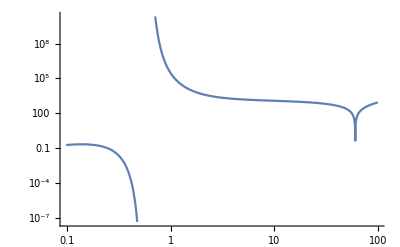

```mathematica
LogLogPlot[Abs[(9.003163161571062*^8 Δ (20.50022583434776 (ⅇ^(-(40.0246913580247 (9.876543209876543*^8 (8.-29 Δ^2)+3200000000000 (1.-3 Δ^2)+6774.035123372113 (0.25-Δ^2)+3048.3158055174513 (2000 Δ^2+8400 (0.25-Δ^2))))/((4000000 (1.-3 Δ^2)+24700.502972107908 (0.25-Δ^2))^2))-(27687.510543582935 ⅇ^(-(3.204940100594422*^7)/(4000000 (1.-3 Δ^2)+24700.502972107908 (0.25-Δ^2))) Δ)/(4000000 (1.-3 Δ^2)+24700.502972107908 (0.25-Δ^2)))+(567600.218934335 ⅇ^(-(3.204940100594422*^7)/(4000000 (1.-3 Δ^2)+24700.502972107908 (0.25-Δ^2))) Δ Erf[(15621.005043058174 Δ)/(4000000 (1.-3 Δ^2)+24700.502972107908 (0.25-Δ^2))])/(4000000 (1.-3 Δ^2)+24700.502972107908 (0.25-Δ^2))+1/(4000000 (1.-3 Δ^2)+2060000 (0.25-Δ^2))20.01234567901235 (2.0676264853703603*^7 ⅇ^(-(3.612*^7)/(4000000 (1.-3 Δ^2)+2060000 (0.25-Δ^2))) Δ+ⅇ^(-(3402. (40000000000 Δ^2+10617.283950617284 (4000000 (1.-3 Δ^2)+2060000 (0.25-Δ^2))))/((4000000 (1.-3 Δ^2)+2060000 (0.25-Δ^2))^2)) (-2060000 (0.25-Δ^2)+4000000 (-1.+3 Δ^2))-2.0676264853703603*^7 ⅇ^(-(3.612*^7)/(4000000 (1.-3 Δ^2)+2060000 (0.25-Δ^2))) Δ Erf[(1.1665333257134149*^7 Δ)/(4000000 (1.-3 Δ^2)+2060000 (0.25-Δ^2))])))/(184502.03250912984 √(1998.1498612395928 Δ^2+40.0246913580247 (0.25-Δ^2)) Erf[4003.086372159875 √(1/(4000000 Δ^2+4942.844078646548 (0.25-Δ^2)))]+20012.345679012345 √((80000 Δ^2)/43+42. (0.25-Δ^2)) Erf[4249.7058721751555 √(1/(4000000 Δ^2+430000 (0.25-Δ^2)))])],{Δ,0,100}]
```